-Graphics3D-

a00.gif

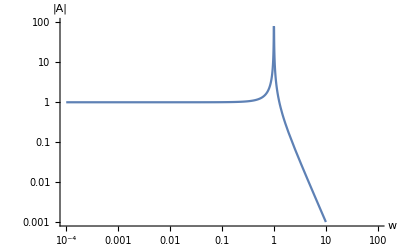

```mathematica
a=0.0;
z[s_]:=1;
n[s_]:=(s+1) (s^2+a*s+1);
H[s_]:=z[s]/n[s];

solZ=Solve[z[s]==0,s]//N;
solN=Solve[n[s]==0,s]//N;

Plot3D[Abs[H[I w+r]],{w,-3,3},{r,-2,0},PlotPoints->50,AxesLabel->{jw,r,"|A|"},PlotRange->{0,5},ViewPoint->{1.3,2.4,2},ImageSize->400]

Export["a00.gif",%,"GIF",ImageSize->300]

LogLogPlot[Abs[H[I w]],{w,0.0001,100},PlotRange->{0.001,100},AxesLabel->{w,"|A|"},ImageSize->400]
```